# Chapter. Basics of Mathematica Programming

##### Paul Abbott paul.c.abbott@uwa.edu.au

Science is what we understand well enough to explain to a computer. Art is everything else we do. — Donald Knuth — Foreword to the book A=B.

## Introduction

Mathematica is a high-level computer language: it has a several thousand built-in functions and operations. This means that for many purposes programming in the traditional sense is not necessary, instead you just use a sequence of built-in functions. This has many advantages, the principle one being the speed of programming — not having to redo the basics saves a lot of time. The built-in functions are highly optimised and very flexible. They are also well integrated with each other and their properties — derivatives, integrals, series, numerics etc — are incorporated into the kernel.

The main behaviour of Mathematica is as an expert system. Knowledge is added in the form of transformation rules and an expression is evaluated by applying these transformations until no more rules apply. But, other powerful programming constructs are also built in, so it is possible to work in a procedural/imperative way, to use the powerful paradigm of functional programming and to use the rules-based method described above. Often a mix of these methods will be employed.

### References

Mathematica Documentation Center ⊳ reference.wolfram.com

Mathematica programming: an advanced introduction ⊳ www.mathprogramming-intro.org

## Structure of Expressions

In Mathematica Everything Is an Expression. This means that everything can be treated the same way.

### Expressions

An expression has two parts: a Head and a Sequence of arguments.

Here is an expression:

```mathematica
f'[x/2]
```

### FullForm

The full (internal) structure of an expression is displayed using FullForm:

```mathematica
FullForm[%]
```

### Atoms

The head and arguments of an expression are also expressions (since everything is an expression). These expressions then have heads and arguments which are expressions. And so on. It stops when all of the inner-most expressions are atoms.

The recursive structure of expressions is nicely displayed in TreeForm:

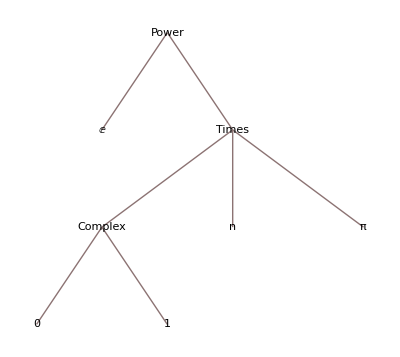

```mathematica
TreeForm[E^(n ⅈ π)]
```

The lowest (-1^th) Level contains all of the atoms from the terminating nodes of the tree:

```mathematica
Level[ⅇ^(n ⅈ π),{-1}]
```

{ⅇ,ⅈ,n,π}

### Types of atoms

Mathematica expressions are built from 3 types of atoms:

Symbol

String

Numbers

Numbers come in 4 “flavours”:

Integer

Rational

Real

Complex

The fact that all expressions have the same basic structure means that operations like Map, Apply, Nest, Fold and all of their friends can be used on any expression. This leads to the paradigm of Functional Programming.

Two enlightening tutorials in the Documentation Center: Expressions and Evaluation of Expressions.

## Function Definitions

Functions definitions are user-defined rules of the form LHS=RHS, where the left-hand side gives the function syntax and the right-hand side gives the rule describing how the arguments should be used in the computation.

By default, user-defined rules are in the global context.

### Functions of one variable

Define a function of one variable: f(x)=5x-1:

```mathematica
f[x_]=5x-1
```

The expression on the left-hand side, f[x_], is a pattern which matches any expression of the form f[any expression].  The _ or Blank makes x a generic variable whose value is passed to the right-hand side of the expression.

Compute f(5) and f(5.0):

```mathematica
f[5]
```

24

```mathematica
f[5.0]
```

24.

Lookup the values associated with a symbol using ?:

```mathematica
?f
```

Global`f

f[x_]=-1+5 x

Symbolic examples:

```mathematica
{f[ξ],f[🐺],f[-Graphics-]}
```

{-1+5 ξ,-1+5 🐺,-1+5 -Graphics-}

It works with vectors (lists) too f:ℝ^n→ℝ^n

```mathematica
f[{x,y,z}]
```

{-1+5 x,-1+5 y,-1+5 z}

Here is a map h:ℝ^2→ℝ^2

```mathematica
h[{x_,y_}]:={x^2-1,(x+y)/2}
```

Omitting the blank in the definition means that the pattern only matches the exact expresion (the expression x):

```mathematica
g[x]=5x-1
```

-1+5 x

```mathematica
{g[x],g[5]}
```

{-1+5 x,g[5]}

Use Clear to clear the values associated with a symbol. Note what happens to the colour of the symbol:

```mathematica
Clear[f,g]
```

The symbol f still exists in the Global` Context but with no definitions (values):

```mathematica
?f
```

Global`f

You can Remove the symbols:

```mathematica
Remove[f,g]
```

```mathematica
?f
```

Information::notfound: Symbol "f" not found.

### Immediate versus Delayed Assignment

Let's see what can go wrong with above if we are not careful.

#### Immediate assignment

Define some value for x:

```mathematica
x=5;
```

```mathematica
x^2
```

25

Define the function f(x)=5x-1 using = or Set:

```mathematica
f[x_]=5x-1
```

24

Try computing f(1). The result is incorrect:

```mathematica
f[1]
```

24

Assignments made using = or Set are immediate assignments. In immediate assignments, the right-hand side of the definition is evaluated first, and then that value is assigned to the pattern on the left-hand side. Since x already had a value, what we really told the computer was that f(x)=24.

Lookup the values associated with a symbol using ?

```mathematica
?f
```

Global`f

f[x_]=24

#### Delayed assignment

Using a delayed assignment ( := or SetDelayed) is the way to resolve this problem.

Use Clear to clear the values associated with a symbol. Note what happens to the colour of the symbol:

```mathematica
Clear[f]
```

Check the value of x:

```mathematica
x
```

5

Define f(x)=5x-1 using a delayed assignment ( := or SetDelayed):

```mathematica
f[x_]:=5x-1
```

Check the value of f(1) and f(t):

```mathematica
f[1]
```

4

```mathematica
f[t]
```

-1+5 t

#### Which type of assignment should one use?

Both types of assignment are required. The difference between immediate and delayed assignments is demonstrated in the following two examples.

Using immediate assignment:

```mathematica
randImmediate=RandomReal[]
```

```mathematica
Table[randImmediate,{3}]
```

Using delayed assignment. Note that the definition generates no output:

```mathematica
randDelayed:=RandomReal[]
```

```mathematica
Table[randDelayed,{3}]
```

### Multiple Definitions

Any symbol can have multiple rewrite rules (or definitions) assigned to it. Which definition is used depends on which pattern is matched. This allows us to write quite powerful rule-based programs.

Define a rule that implements the log of a product (valid for positive x and y):

```mathematica
log[x_ y_]:=log[x]+log[y]
```

Check the rule:

```mathematica
?log
```

Global`log

log[x_ y_]:=log[x]+log[y]

Check that this rule works:

```mathematica
log[a b]
```

log[a]+log[b]

```mathematica
log[a^2]
```

log[a^2]

It works for a product of more terms:

```mathematica
log[a b c]
```

log[a]+log[b]+log[c]

This is because multiplication (Times) is associative:

```mathematica
Attributes[Times]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
Trace[log[a b c]]
```

{log[a b c],log[a]+log[b c],{log[b c],log[b]+log[c]},log[a]+(log[b]+log[c]),log[a]+log[b]+log[c]}

It automatically knows about rational expressions:

```mathematica
log[a/b]
```

log[a]-log[b]

Use FullForm to see why:

```mathematica
FullForm[a/b]
```

Times[a,Power[b,-1]]

What about this case?

```mathematica
log[a a]
```

log[a^2]

What about this case?

```mathematica
log[2/3]
```

log[2/3]

Define a rule that implements log of a power:

```mathematica
log[x_^n_]:=n log[x]
```

Check the rules:

```mathematica
?log
```

Global`log

log[x_ y_]:=log[x]+log[y]
 
log[x_^n_]:=n log[x]

Expand out log(a b^3 c d^e):

```mathematica
log[4a b^3 c d^e]
```

log[4]+log[a]+3 log[b]+log[c]+e log[d]

## Programming Styles

Consider the factorial function (built-in as Factorial). For natural numbers,

n!==n(n-1)(n-2)⋯2×1

This definition can be thought of as the solution to the recursion relation

n!==n×(n-1)!
 0!==1

Note that n! is continued to complex numbers by the Euler Gamma function Γ(n+1)=n!

### Built-in Function

Compute n! for n=0,1,…,10:

```mathematica
facs=Table[{n,n!},{n,0,10}]
```

(0 | 1
1 | 1
2 | 2
3 | 6
4 | 24
5 | 120
6 | 720
7 | 5040
8 | 40320
9 | 362880
10 | 3628800)

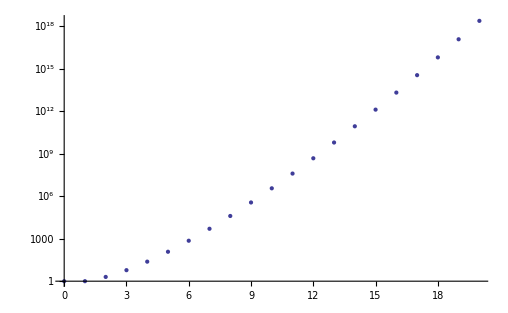

```mathematica
ListLogPlot[Table[{n,n!},{n,0,20}]]
```

### Procedural Programming

Procedural Programming is the ‘traditional’ form of programming used in languages such as Basic, Fortran, C, Java etc… In this style the programmer directs exactly how the computation/program is to proceed. This is done with all the standard constructs: Inputs/Outputs, Assignments , Loops , Conditionals  etc.  The primary advantage of (a compiled) procedural program is speed. A good programmer can write a very efficient program, and in fact the lower level language the program is written in the more efficient it can be. The ultimate in efficiency comes from programming directly in assembly, but that's not much fun (Mathematica itself is primarily written in C).

For more specialised and optimised problems, (or if you want to reuse old code that you have) Mathematica also has MathLink, .NET/Link and J/Link for linking (in both directions) to C, .NET and Java programs respectively. It can also simply Run external commands, then Import the output.

In general, procedural code uses a scoping construct, eg Module, which defines a local environment where more complicated subroutines can be run using local, temporary variables.  And Looping Construct(s) such as Do, While or For.  In fact, familiar commands like Table are basically a Do loop, where the intermediate results are stored.

#### facProcedural

Here's a couple of ways of coding the factorial function in a procedural manner:

```mathematica
facProcedural1[n_]:=
Module[{i=1,s=1},
While[i<n,i++;s=i*s];
s]
```

```mathematica
facProcedural2[n_]:=
Module[{s=1},
Do[s=i*s,{i,1,n}];
s]
```

Test these procedures for n=5:

```mathematica
facProcedural1[5]==facProcedural2[5]==5!
```

True

#### Checks and Timing

Time and test these procedures for n=10^4:

```mathematica
(10^4)!
```

28462596809170545189064132121198688901480514017027992307941799942744113400037644437729907867577847758158840621423175288300423399401535187390524211613827161748198241998275924182892597878981242531205946599625986706560161572036032397926328736717055741975962099479720346153698119897092611277500484198845410475544642442136573303076703628825803548967461117097369578603670191071512730587281041158640561281165385325968425825995584688146430425589836649317059251717204276597407446133400054194052462303436869154059404066227828248371512038322178644627183822923899638992827221879702459387693803094627332292570555459690027875282242544348021127559019169425429028916907219097083690539873747452483372899521802363282741217040268086769210451555840567172555372015852132829034279989818449313610640381489304499621599999359670892980190336998484404665419236258424947163178961192041233108268651071354516845540936033009607210346944377982349430780626069422302681885227592057029230843126188497606560742586279448827155956831533440534425446648416894580425709461673613187605234982286326452921529423479870603344290737158688499178932580691483168854251956006172372636323974420786924642956012306288720122652952964091508301336630982733806353972901506581822574295475894399765113865541208125788683704239208764484761569001264889271590706306409661628038784044485191643790807186112370622133415415065991843875961023926713276546986163657706626438638029848051952769536195259240930908614471907390768585755934786981720734372093104825475628567777694081564074962275254993384112809289637516990219870492405617531786346939798024619737079041868329931016554150742308393176878366923694849025999607729684293977427536263119825416681531891763234839190821000147178932184227805135181734921901146246875769835373441456013122615221391178759688367364087207937002992038279198038702372078039140312368997608152840306051116709484722224870389199993442071395836983063962232079115624044250808919914319837120445598344047556759489212101498152454543594285414390843564419984224855478532163624030098442855331829253154206551237079705816393460296247697010388742206441536626733715428700789122749340684336442889847100840641600093623935261248037975293343928764398316390312776450722479267851700826669598389526150759007349215197592659192708873202594066382118801988854748266048342256457705743973122259700671936061763513579529821794290797705327283267501488024443528681645026165662837546519006171873442260438919298506071515390031106684727360135816706437861756757439184376479658136100599638689552334648781746143243573224864326798481981458432703035895508420534788493364582482592033288089025782388233265770205248970937047210214248413342465268206806732314214483854074182139621846870108359582946965235632764870475718351616879235068366271743711915723361143070121120767608697851559721846485985918643641716850899625516820910793570231118518174775010804622585521314764897490660752877082897667514951009682329689732000622392888056658036140311285465929084078033974900664953205873164948093883816198658850827382468034897864757116679890423568018303504133875731972630897909435710687797301633918087868474943633533893373586906405848417828065196275826434429258058422212947649402948622670761832988229004072390403733168207417413251656688443079339447019208905620788387585342512820957359307018197708340163817638278562539516825426644614941044711579533262372815468794080423718587423026200264221822694188626212107297776657401018376182280136857586442185863011539843712299107010094061929413223202773193959467006713695377097897778118288242442920864816134179562017471831609687661043140497958198236445807368209404022211181530051433387076607063149616107771117448059552764348333385744040212757031851527298377435921878558552795591028664457917362007221858143309977294778923720717942857756271300923982397921957581197264742642878266682353915687857271620146192244266266708400765665625807109474398740110772811669918806268726626565583345665007890309050656074633078027158530817691223772813510584527326591626219647620571434880215630815259005343721141000303039242866457207328473481712034168186328968865048287367933398443971236735084527340196309427697652684170174990756947982757825835229994315633322107439131550124459005324702680312912392297979030417587823398622373535054642646913502503951009239286585108682088070662734733200354995720397086488066040929854607006339409885836349865466136727880748764700702458790118046518296111277090609016152022111461543158317669957060974618085359390400067892878548827850938637353703904049412684618991272871562655001270833039950257879931705431882752659225814948950746639976007316927310831735883056612614782997663188070063044632429112260691931278881566221591523270457695867512821990938942686601963904489718918597472925310322480210543841044325828472830584297804162405108110326914001900568784396341502696521048920272140232160234898588827371428695339681755106287470907473718188014223487248498558198439094651708364368994306189650243288353279667190184527620551085707626204244509623323204744707831190434499351442625501701771017379551124746159471731862701565571266295855125077711738338208419705893367323724453280456537178514960308802580284067847809414641838659226652806867978843250660537943046250287105104929347267471267499892634627358167146935060495110340755404658170393481046758485625967767959768299409334026387269378365320912287718077451152622642548771835461108886360843272806227776643097283879056728618036048633464893371439415250259459652501520959536157977135595794965729775650902694428088479761276664847003619648906043761934694270444070215317943583831051404915462608728486678750541674146731648999356381312866931427616863537305634586626957894568275065810235950814888778955073939365341937365700848318504475682215444067599203138077073539978036339267334549549296668759922530893898086430606532961793164029612492673080638031873912596151131890359351266480818568366770286537742390746582390910955517179770580797789289752490230737801753142680363914244720257728891784950078117889336629750436804214668197824272980697579391742229456683185815676816288797870624531246651727622758295493421483658868919299587402095696000243560305289829866386892076992834030549710266514322306125231915131843876903823706205399206933943716880466429711476743564486375026847698148853105354063328845062012173302630676481322931561043551941761050712449024873277273112091945865137493190965162497691657553812198566432207978666300398938660238607357858114394715872800893374165033792965832618436073133327526023605115524227228447251463863269369763762510196714380125691227784428426999440829152215904694437282498658085205186576292992775508833128672638418713277780874446643875352644733562441139447628780974650683952982108174967958836452273344694873793471790710064978236466016680572034297929207446822322848665839522211446859572858403863377278030227591530497865873919513650246274195899088374387331594287372029770620207120213038572175933211162413330422773742416353553587977065309647685886077301432778290328894795818404378858567772932094476778669357537460048142376741194182671636870481056911156215614357516290527351224350080604653668917458196549482608612260750293062761478813268955280736149022525819682815051033318132129659664958159030421238775645990973296728066683849166257949747922905361845563741034791430771561168650484292490281102992529678735298767829269040788778480262479222750735948405817439086251877946890045942060168605142772244486272469911146200149880662723538837809380628544384763053235070132028029488392008132135446450056134987017834271106158177289819290656498688081045562233703067254251277277330283498433595772575956224703707793387146593033088629699440318332665797514676502717346298883777397848218700718026741265997158728035440478432478674907127921672898523588486943546692255101337606377915164597254257116968477339951158998349081888281263984400505546210066988792614558214565319696909827253934515760408613476258778165867294410775358824162315779082538054746933540582469717674324523451498483027170396543887737637358191736582454273347490424262946011299881916563713847111849156915054768140411749801454265712394204425441028075806001388198650613759288539038922644322947990286482840099598675963580999112695367601527173086852756572147583507122298296529564917835071750835741362282545055620270969417476799259229774888627411314587676147531456895328093117052696486410187407673296986649236437382565475022816471926815559883196629848307776666840622314315884384910519058281816740764463033300119710293036455866594651869074475250837841987622990415911793682799760654186088721626654886492344391030923256910633775969739051781122764668486791736049404393703339351900609387268397299246478483727274770977466693599784857120156789000241947269220974984127323147401549980920381459821416481176357147801554231599667838534854486406936410556913531335231184053581348940938191821898694825383960989942822027599339635206217705343572073396250574216769465101608495601439303244304271576099527308684609204422226103154229984444802110098161333824827375218998738205315164927134498105950159974800571591912202154487748750103473246190633941303030892399411985006225902184164409988173214324422108554248620896250260604398180189026317781146617454999771440665232863846363847001655618153861098188111181734191305505024860345856755585637511729774299329074944236579668332700918367338977347901759248885660379952771540569083017311723894140326159612292912225191095948743805673381278538616491842786938417556898047100859868372033615175158097022566275200160956192229925401759878522038545913771783976389811198485803291048751666921195104514896677761598249468727420663437593207852618922687285527671324883267794152912839165407968344190239094803676688707838011367042753971396201424784935196735301444404037823526674437556740883025225745273806209980451233188102729012042997989005423126217968135237758041162511459175993279134176507292826762236897291960528289675223521425234217247841869317397460411877634604625637135309801590617736758715336803958559054827361876112151384673432884325090045645358186681905108731791346215730339540580987172013844377099279532797675531099381365840403556795731894141976511436325526270639743146526348120032720096755667701926242585057770617893798231096986788448546659527327061670308918277206432551919393673591346037757083193180845929565158875244597601729455720505595085929175506510115665075521635142318153548176884196032085050871496270494017684183980582594038182593986461260275954247433376226256287153916069025098985070798660621732200163593938611475394561406635675718526617031471453516753007499213865207768523824884600623735896608054951652406480547295869918694358811197833680141488078321213457152360124065922208508912956907835370576734671667863780908811283450395784812212101117250718383359083886187574661201317298217131072944737656265172310694884425498369514147383892477742320940207831200807235326288053906266018186050424938788677872495503255424284226596271050692646071767467502337805671893450110737377034119346113374033865364675136733661394731550211457104671161445253324850197901083431641989998414045044901130163759520675715567509485243580269104077637210998671624254795385312852889930956570729218673523216666097874989635362610529821472569482799996220825775840988458484250391189447608729685184983976367918242266571167166580157914500811657192200233759765317495922397884982814705506190689275625210462185661305800255607974609726715033327032310025274640428755556546883765838802543227403507431684278620637697054791726484378174446361520570933228587284315690756255569305558818822603590006739339952504379887470935079276181116276309771257983975996526612120317495882059435754883862282508401408885720583992400971219212548074097752974278775912566026443482713647231849125180866278708626116699989634812405803684794587364820124653663228889011636572270887757736152003450102268890189101673572058661410011723664762657835396364297819011647056170279631922332294228739309233330748258937626198997596530084135383241125899639629445129082802023225498936627506499530838925632246794695960669046906686292645006219740121782899872979704859021775060092893328957272392019589994471945147360850770400725717439318148461909406269545285030526341000565022226152309364882887122046454267700577148994335147162504252365173710266068647253458120186683273953682547456536553597546685788700056988360286686450740256993087483441094086086303707908295240576731684941855810482475304758923392801571302824106234999945932390521409856559565661346003396150515164758852742214732517999548977992849522746029855666700811871200856155016457400484170210303038996339253337466556817824410737409336919294104632307731994759826307383499600770372410446285414648704116273895649834555162165685114551383822047005483996671706246467566101291382048909121117229386244253158913066987462045587244806052829378148302622164542280421757760762365459828223070815503469404938317755053305094698999476119419231280721807216964378433313606760676965187138394338772485493689061845700572043696666465080734495814495966306246698679832872586300064215220210171813917325275173672262621454945468506006334692713838311715849753092643252486960220059099802663765386225463265168414963306369548086551101256757717890616694758344043486218485369591602172030456183497524162039926441331651884768606830642004858557924473340290142588876403712518642229016333691585063273727199596362912783344786218887871009533753551054688980236378263714926913289564339440899470121452134572117715657591451734895195016800621353927175419843876163543479806920886666227099512371706241924914282576453125769939735341673046864585181979668232015693792684926999983992413571941496882273704022820805171808003400480615261792013978945186295290558440703738300533552421153903385185829366779190610116306233673144419202893857201855569596330833615450290424822309297087124788002017383072060482680156675397593789931793515799958929562156307338416294599900276730832827716595064217966523190439250543226753731811755315476780739470338931185107297724318378972674957455778183345495942317353558291046967315391275975687281861691161083156337232639968881490543943261197182274996791176628553401860198315809629981791107208804992292016062059067271273599461871634945774995805337947187105456452579396024210259136415528398395201773012712514892051061708228008339985665786646920737114269682301770416324829479409558694699089379165191006305185352102345189798127619143061864362703081977124992751056732909481202057747100687703379708934229207183903744167503493818836342229284946790660285674293251642569044363473087656797056595677285291081242733154406580199802711579126254172797452862574865921933293805915239524735518887119860391319654287576290190503964083560246277534314409155642181729459941596061979622633242715863425977947348682074802021538734729707999753332987785531053820162169791880380753006334350766147737135939362651905222242528141084747045295688647757913502160922040348449149950778743107189655725492651282693489515795075486172341394610365176616750329948642244039659511882264981315925080185126386635308622223491094629059317829408195640484702456538305432056506924422671863255307640761872086780391711356363501269525091291020496042823232628996502758951052844368177415730941874894428065427561430975828127698124936993313028946670560414084308942231140912722238148470364341019630413630736771060038159590829746410114421358321042574358350220737173219745089035573187350445827238770728271406162997919629357224104477155051652535867544109395079218369015261138440382680054150924346511711436477899444553993653667727589565713987505542990824585609510036934663100673714708029927656933435500927189854050109917474979991554392031908961967615444686048175400695689471463928245383807010444181045506171305160584355817521032338465829201071030061124283407458607006060194830551364867021020364708470807422704371893706965688795617928713045224516842027402021966415605280335061293558739079393524404092584248380607177444609964035221891022961909032569042381374492494906892314330884224399631396391545854065286326468807581148748371408284176455226386313520264894016262494802388568231599102952620337126449279901938211134518446387544516391239377974190576649911764237637722282802318465738050121277809680315691477264910257503508758792248110223544524410872448565700755187132146592093548504552829170749596775404450779494836371756062326925757412813110241910373338080434325310884694831555729402265394972913817581338619457057799561808755951413644907613109617155928376585840036489374076822257523935988731081689667688287403837192827690431514106997678303819085690713091931340846019511147482766350724676534922040058626677632935516631939622498979912708004465982264899125226813124300528104995058595676527123591494442612554437618645029202881358582871789577224116380815161831603129728796987480139828621645629196153096358337313619724773332353025466571196902611237380629030242904275794549030022660847446513161741691916851746464945459696005330885252792083472495235473110674109099223541055506299687642153951249355986311346661725116890785633328935569150449485189113488301876365100638502565916433021928565596263914382895068324838727165616560111531517055222955765944972454788815532316417453267167978861141165355597588331979638070962998880767303616940317736448140427867784251232449974693421348217179595190698204602997172001174857303889719205597414742453011135869766256607770970225633261701108463784795555258504578058879440756064974127974530918418405207558526462208821483646754652237609210787539190454684852349759986044943322828073120679922402477507514105890774627334319091255451352225329275913842047384603056163154236552935312278389759446515787337343463172280001031380425481404022090580405056003860937403435068863081434683848900708938565050027569059678069404698435184535134141031615133683043714786642925389717165978629010728400758939700388317742648163725113277369926827709465342583596111881955092462062153978121197244762623771534452048069819082524943963962251113831177428978535825590832490480497516047104257569753442551515779815600370847230603484753977513688390404316017486248871339311818523029425425676202485688393970836748788453789172574145155917919035398535077200900594979352939459631213445503368260690059828717723533375221941915547303742062343262892968397015058892191112049249864792053410872349115430987182160055762209075732304626106597744947658346313025598636315029959672352476943975462530206788193304372284800209305354155640664838569378144603138697563459200233462606995955513484754147891180830329816421587452922952678937925647752029052675349356673744293182673374571642465407748267901046778759085408130531447176455869894169668940436489952465247443988349583871206296485413357553813419500498743813369062703973874586604296871595820715766599826607317005624465541763024501349159567288942619746144496908671655859782729228702723774835097362901019130417812735773037781804081589136005207315806941034305003184349342360269244733060013861119781774472669608928321052543116496033420102032603863672532889648333405862204843616575362001468405476649666473566979572953394809138263703324220930839366954980688240491622063147911494642042500022450413425558561937442905257252436320054487441524307305215070491020434076572476865095751174125413729531644521765577235348601821566833352520532830000108344008762266843817023235605645158256954177359197813649975559601912567744942717986360045847405209290089397315276024304951653864431388147876977541478757432610159879709758855625806766197973098472460769484821127948427976536607055051639104415022554420329721292033009353356687294595912327965886376486894188433640548494009574965791657687213927330153555097865114767947399690623184878377515462613823651665956337209345708208301840482797005728071432925727577436229587047361641609731817241594204270366066404089740245521530725227388637241859646455223673260411164598464020010216920823315155388821071527191267876531795071908204525100447821291318544054814494151867114207103693891129125012750853466337717749376016543454696390042711129829255096830420665725364279472200020835313883708781649957189717629338794854271276882652003766325924561614868744897471519366219275665852462114457407010675380427564184440834805203838265052601698584060084788422421887856927897751810442805474427229455167420335686460609977973124950433321425205053675790499520783597650415379001132579536040655172654879022173595444151139429231648950663177813039057462082449171921311864129633704661406456900178942356738775523130952785912774533241855442484484493664210731348819180640189222317302156645813473186449997905781662091469870718039388885781280740226363602294114354869871402143572055947730892808653678920201935102605361567924483276749476117858316071865710310842200560259545115191391309119544447844361032741876102338843391687589233423790859841968266525610628751237572318491474951945985728897934981791761822652480408237128109790772638864286067917082288575852703470839714561619926247844794692794996845945632382702297364173503430783194115698247820013290851202878474805860188960045901745974055630732714487679085288867978809970695240681006625611440014983413580889737246844064948857074167687916413224205373654067330186392497910915474785959163865597507090581175924899502214799250945635582514315814464060134283490422798357939659258985200763845646681640732681928346007767285876284900068874564639274964415904034033672337814491597032941787294155061054129515400159393851663929325677429557549480046658273579653990940233543644649376827272541873627547532976808190325336141086433084237771738995221536763095302045902438694632702895293994483013577589081214884558493819874505920914067209522469096263076941753340983698859363700314973728977996360018626500174929290087931189997822963712306642297996163582572600112288983647651418045975770042120833949364659647336464289044499325396227091907373705772051322815957863227591912786054297862953188615559804728160710864132803585400160055575686855791785977899197902656592621283007225351401525973569300729015392211116868504740402172174442051738000251361000494534119324331668344243125963098812396962202358858395587831685194833126653577353244379935683215269177042249034574534858913812582681366908929476809052635560638119661306063936938411817713545929884317232912236262458868394202889981693561169865429884776513118227662526739978808816010470651542335015671353744817086234314662531190291040152262927104099285072418843329007277794754111637552176563589316326636049381218401837512818884771168975479483767664084842753623074019542183217985496260666590347925816342392670947839907062923166535037285019751324813803837070894638925470887039085723581006130628646664710006104352115778926613432214655311411882596942926284522109026688414975763341554921135581254616558078273470115814006008345762133130389987843270653719956709570847385786092649188858378739239165554263577301292243641604062551736892335636568854365851646207821875741724364525814143487632761341752707376754922276287782264765154315341585713773522730335403376364204258034257264749686217823666951353410677378421131371131987373222891805275062812277716412494412401207125954319991746574745892582613712825555535080404143944557295994554635608487251339462936358940832098964801619583130429720964794128539388996265368928263807677168759588502216464582430940165009688797366157733560316836710386895228270941509545222744002735499253670214715994056544813842186380128799900820933576320736369405991424263718294000613741900579513096298545330748197802568301089672873802234820488862973130369689882640657904781562389778485365025691064231795736025330908763271784911189748432246868086340383964176127605788646574472284824932687443062551220506955168464669477183681911432873544815836350548146411099960143390595799766290646881295025039150923633011076070632863317393378149693380247580035052789782755750928604039420506342939327064636161031822879248152679306862749237275631852225654266008556849497720285909150930495425967473648331437236349555448901598668408362176913559656039519670425368863482369587129462524759031776813184977588276576740482558136502103649585505703259219957675334264223783723586058509403583977103476670644788640831109650302565215607464019652716999732373465237173456595514559493098166644006211599349133180135150528651842178828026343325934755850761168697709125580056185683710540856081249519403148064618719402577663285267019698387567561524696759028106864896869293315954352097687527137201616160931174250199709289684940034696242325688410665113304377412256176258658941236728171145526423894512631717834790276921171452887352955019336759218908006048633737786728180610254782570436788449503518925787499836694785908612975543084122677060954347612133717433156783790162012337237023338316414706428592185977610158232721997915062871868186750981665537745013020880333904353639770263363809098526494532628146558065546504823486429495390613257400496912888340518222933644476683855037967975809619983575807027759535968788226194659612223044549275600274955168583542582295336042834426318478068825395450746691877897765406038432512843812811316856204608617289408229658626174420766920297427930088129519854678713548623236610413216581279267151545961594352593456757445992307889205519540082316409719591250025455237503106735639748835542480449681383030671851931491335789202123605308199952020584503423499932150962634977812456658304680581824563524814625849331926195406884818446445248429486063016169476663242625231476322371109695369483824482316410396224507675405614287468267835723704895606990652792688455844512046654853378534026646645042339638488257719874953611300494215593735545211926186721478265416885604094928290056616883807637656690510740892510549165222968878676968631652514917701499900066637344546120262780701925698706225540928945194718778004306130021828287425867048748480826948573444778244078734102710824870269523830804910960482013901294024631244800159336670212658317677879752965963472576894326540435889267293950687860830626266263287392087327302547910099932113388977807814336728791448768373686467748528777737403547472871644217767820712964506270880978637928144071192505141148004907055608097229299792441471062852247029870699869227676341773513258602908903875707454368077876422385333700692089616351009233587303986543906071880952557553380364725895007306772122528078179471056481171378557451057691044322925429024149433588396093679321361696954251299731031032804436954501929843820842383121265825740594509426942777307124802176915781835720087170538773256017987133005505911377823841791640280841409623820847637393013930778428554545222367559824666250608754284876104145661362227642405914304455580856318180935230407793891614902116292400515074914068443203230365609954878620999194306564455332547135557365318516011700321550690787716752062881527885897149410320986984083048966524351030502444679931779147659103428949129054120361601695671222140806369405940304552186212879933092856231022418446365289097444640151986623183881962444822590783585914043686193019041458962693878907034982169868696934448086213990534591792826654304798207219634134755646525483143771156678459077797196510772468000293581546267646310224279007313631352522067062951125935874473134186492497282784796644585448962932905262058065248588707020879389134476083344653170939242408249328008915731319541348311820927752486880548733943315867562666122179355051190609992911379445634995627391898459029021713155706096267881673302940198464237390445098028030948975981259252055850973537436556825780313681902007151675693827281818824587541710721180806556448039122504537089422695358382192535075692834095639859265599740391316709290043996275976830375217503360879028295673068862263077729733533853682668734519035709709687322323738300494090123239274318759046526327095178406267264828893646896593219169521106361729757074376148061601331104911692271318609404145014842866423634716982892418180484365230538864559809839273836490685480823014267803143937440431807822678779494006206489151248952516543005634448375046751754207043313372486870633237561645232360481932024377596890914783372179553676992603235715185513391098402739063753280702313301755754269396202629423910945323537910125948964941812563672992967084250667599803456273455598559628512281414582556024841783305645240508450065988755987518601335860624932784487772006842296591945516539562982960591610046578907214842054861830418175604559815168088031783080261445994444677918012432146400983610678683412974872596729258786806223080115822026289014364459002301645823666709265571264559925790622304745235625575111770791512002789380975775468546121017307522799241407026308137792971909461413145802081087738121624539858769697371425881836152605069380926917712087321915005831977113322793572385071940612761291872572099404930250277748156614021327434743881966413330052634229082906400927944924808556131183440161804801357032507836323938921567643159620442612809700944107776130638909071294456394056601559246025454204771186140420155233371270501377121034570009578009389265329385720478576508777149663403003562380595757191609382171312222810465858388943507176431939973012661591423837170284400120399485880996231859472474858776584355077006934099220340378772192728370301380838144394114984971730766162961342059105014814283949700695951676939041557902856356911055547312684571497449635320554677940775184056667637222969090346128706829887104278761090090999160443821794511763620835379716161833124364431267855435550800507986124664397724135502128238026726719914989727248512981287283697489276420792868666970177259794407858155909332508554131299946581118527691652464790819119384233275897699573012098103009171001695718791616942270079528915191912521053891838538959315167400505723817401030621004380243011187977704252328073236575129609372456053680037516596164236147709330391224409752871732067976128120428026739256557305675931512645750047875756531854825821411574030473147492511910835615765732002546109686701890307648531373832912682481741181359032826625082549313211431478953352317043989053928534946642886074268371824902498092479487226633686823799580875637040808655649321905489637785549531167397935270799470452399153297534358690514105864096534514182896474439367182852711843560799285895978176543950113088848419163516673213692860830956744502801800373716458009168082972708715609185038654053436660045504985624687376022557041595800250174095361839287643458003670864954057941720085136357127163768323493134230703821274484501440529541695374381945459456533165140990993722722801019654652726227831512103467686166826131471843610025517863247950150022953695466317739589344131481485834694374523981159954666071205997794363440185078360899108948073419633939259318973940943110042116729120199722626609871927014024105805515315100109804996044147291039451030312664114726736839973315035036742741546992633165270432940675237449075056739508929674779115800864399992564817208847429250821546279856079127768611946086210349405535850134472190244543824521089284409498132717010673966471114931896789977661595488186193176900175027901783824624387873831483279500879026433992577026588005849778984624295660321276945810824348129690840972550671054732471317254997191901039553305847040728081693158626093886019147689944137673621432083607375131574376316754666479186753896571555100850626810005119827486807780592667765654100834778571024250133253391587384761024129794736751001163498977803745930025457609870671092153597115178252014281216647543034075128600240297038428615984289816602143429849088917359682192284469123035904329877231843309914187264674607558318725713138832356015809009594182530207799397648462597901883341793830920965841463574411985878296475850943053008148341821747826603773762252997703468752903517310792083220038080809212164346586817989810504274375385786789186350517717501606531826406928883250135919517178537687865881752366421534010961295763074762648070312757365787762352859057153932484576503944390496668087711899192498933896524852395536795827530614167131757915756386606004839994179548705868209201195154952031294562451315422506574858629161606523796643010172693950282294667489681746821163996794950294284013099235901278250437428192557634533217576162292751110598368271567229778620053722932314082887058749444060116236521627717558503013451471452765841864277071769968435499620257547431811994883385806759692359580622165832464092095350648357935817742903018315351290014321495518177456908388719320697769695657771754499149911431368950836160692539606469893374870942933219185601299108564470256257163505508620689240297589684714283678684735455533583477652536156578189996983068654671736445996343136468195427420490472433064675001442697508322369013083895492637066778406531328664886080129513771720847581157719491012345141774941482773580041432667332379617716965698582785832300505265883502247868050648201444570593197343382923860072601696510903258980909912837652275381493529845099414966933862815568031306981064525192703818515872648691762563239441425216118427769145067718411735714396681005615483952443154944864238384298900399826113322468963346522104692545137969276009719645338955332105584245640187448611050959111766828942711640054010503770420346052521318228045892998637903572350665108782350043349942391285236308896510989246641056331584171142885304143772286629832318970869030400301325951476774237516158840915838059151673504519131178193943428482922272304061422582078027829148070426761629302539228321084917759984200595105312164731818409493139800444072847325902609169730998153853939031280878823902948001579008000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
Timing[facProcedural1[10^4]==(10^4)!]
```

{0.041042,True}

```mathematica
Timing[facProcedural2[10^4]==(10^4)!]
```

{0.026862,True}

#### Disadvantages

The disadvantages of procedural programming include:

unnecessary dummy variables often need to be introduced; the above example has the two classic dummy variables: a counting variable “i” and a ‘subtotal’ variable “s”;

generalisation, such as to higher dimensions or symbolic arguments, is not always straight forward;

Mathematica is designed for rule-based and functional programming and its code for it is highly optimised. Thus in Mathematica, procedural programming is often the slower option.

### Rule-based Programming

For many situations Rule-Based Programming is often the simplest and most elegant.

#### facRule

Here is a rule-based program for computing n!:

```mathematica
Clear[facRule]
```

```mathematica
facRule[n_]:=n facRule[n-1]
```

```mathematica
facRule[0]=1
```

1

Compute 100!

```mathematica
facRule[100]==100!
```

True

What happens if the argument is not a positive integer?

```mathematica
facRule[-3]
```

$RecursionLimit::reclim: Recursion depth of TraditionalForm`256 exceeded.

-3 (-4 (-5 (-6 (-7 (-8 (-9 (-10 (-11 (-12 (-13 (-14 (-15 (-16 (-17 (-18 (-19 (-20 (-21 (-22 (-23 (-24 (-25 (-26 (-27 (-28 (-29 (-30 (-31 (-32 (-33 (-34 (-35 (-36 (-37 (-38 (-39 (-40 (-41 (-42 (-43 (-44 (-45 (-46 (-47 (-48 (-49 (-50 (-51 (-52 (-53 (-54 (-55 (-56 (-57 (-58 (-59 (-60 (-61 (-62 (-63 (-64 (-65 (-66 (-67 (-68 (-69 (-70 (-71 (-72 (-73 (-74 (-75 (-76 (-77 (-78 (-79 (-80 (-81 (-82 (-83 (-84 (-85 (-86 (-87 (-88 (-89 (-90 (-91 (-92 (-93 (-94 (-95 (-96 (-97 (-98 (-99 (-100 (-101 (-102 (-103 (-104 (-105 (-106 (-107 (-108 (-109 (-110 (-111 (-112 (-113 (-114 (-115 (-116 (-117 (-118 (-119 (-120 (-121 (-122 (-123 (-124 (-125 (-126 (-127 (-128 (-129 (-130 (-131 (-132 (-133 (-134 (-135 (-136 (-137 (-138 (-139 (-140 (-141 (-142 (-143 (-144 (-145 (-146 (-147 (-148 (-149 (-150 (-151 (-152 (-153 (-154 (-155 (-156 (-157 (-158 (-159 (-160 (-161 (-162 (-163 (-164 (-165 (-166 (-167 (-168 (-169 (-170 (-171 (-172 (-173 (-174 (-175 (-176 (-177 (-178 (-179 (-180 (-181 (-182 (-183 (-184 (-185 (-186 (-187 (-188 (-189 (-190 (-191 (-192 (-193 (-194 (-195 (-196 (-197 (-198 (-199 (-200 (-201 (-202 (-203 (-204 (-205 (-206 (-207 (-208 (-209 (-210 (-211 (-212 (-213 (-214 (-215 (-216 (-217 (-218 (-219 (-220 (-221 (-222 (-223 (-224 (-225 (-226 (-227 (-228 (-229 (-230 (-231 (-232 (-233 (-234 (-235 (-236 (-237 (-238 (-239 (-240 (-241 (-242 (-243 (-244 (-245 (-246 (-247 (-248 (-249 (-250 (-251 (-252 (-253 (-254 (-255 (-256 (-257 Hold[facRule(-257-1)]))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))))

Restrict the rule to positive arguments using Condition:

```mathematica
Clear[facRule]
```

```mathematica
facRule[n_/;n>0]:=n facRule[n-1]
```

```mathematica
facRule[0]=1
```

1

```mathematica
facRule[1/2]
```

1/2 facRule(-1/2)

#### $RecursionLimit

Note, however, that recursive programs can exceed $RecursionLimit:

```mathematica
facRule[255]
```

$RecursionLimit::reclim: Recursion depth of TraditionalForm`256 exceeded.

3350850684932979117652665123754814942022584063591740702576779884286208799035732771005626138126763314259280802118502282445926550135522251856727692533193070412811083330325659322041700029792166250734253390513754466045711240338462701034020262992581378423147276636643647155396305352541105541439434840109915068285430675068591638581980604162940383356586739198268782104924614076605793562865241982176207428620969776803149467431386807972438247689158656000000000000000000000000000000000000000000000000000000000000000 Hold[facRule(1-1)]

Increase the recursion limit:

```mathematica
$RecursionLimit=10^5;
```

```mathematica
Timing[facRule[10^4]==(10^4)!]
```

{0.042948,True}

#### Comments

The recursive program could be used in any programming language, but a rule-based approach only works in systems like Mathematica that apply a global rule base to each expression.

Rule based programming can be compared to proof by induction: you only need to worry about how to do the extremal cases and the canonical step(s).

For programs with large sets of replacement rules, a significant increase in speed can be obtained using Dispatch.

### Functional Programming

Functional Programming is a programming style in which the core operation is the application of functions to data and to other functions.  The concept of functions and data is blurred: functions are just an abstract type of data and (just like normal data) can be passed other to functions, and data is just a function that returns itself.  Since all data can be ultimately represented as (nested) lists, functional programming is just the application of functions to and the manipulation of lists.

Since everything in Mathematica is an expression, functional methods are completely general. Functional methods are also very concise, and in Mathematica, they are also normally the fastest method.

#### Factorial

A functional algorithm for calculating n! can be stated as multiply together all numbers from 1 to n.

Use Range to get the numbers 1 to n:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Multiply them together; Apply the Times operation to the above list:

```mathematica
Apply[Times,%]
```

3628800

```mathematica
%==10!
```

True

#### facFunctional

This is easily converted into a procedure:

```mathematica
facFunctional[n_]:=Times@@Range[n]
```

```mathematica
Timing[facFunctional[10^4]==(10^4)!]
```

{0.005469,True}

Using FoldList instead of Apply, we can efficiently generate a whole table of factorials in a single pass:

```mathematica
FoldList[f,x,{a,b,c,d}]
```

{x,f(x,a),f(f(x,a),b),f(f(f(x,a),b),c),f(f(f(f(x,a),b),c),d)}

```mathematica
FoldList[Times,1,Range[10]]
```

{1,1,2,6,24,120,720,5040,40320,362880,3628800}

### Dynamic Programming

Dynamic Programming consists of writing a program that can dynamically modify itself as it runs. In Mathematica this amounts to having a program that define new rules on the fly. In simple cases like our example of n!, new rules basically mean the program saves intermediate results, so it only needs to calculate them once (very important for one of the assignment questions).

The syntax for this is: f[n_]:=(f[n]=…) but, due to operator precedence, we can drop the parentheses.

#### facDynamic

Use dynamic programming to compute n!

```mathematica
facDynamic[n_]:=(facDynamic[n]=n facDynamic[n-1])
```

```mathematica
facDynamic[0]=1;
```

Compute 5!

```mathematica
facDynamic[5]
```

120

```mathematica
Trace[facDynamic[10]]
```

{facDynamic(10),facDynamic(10)=10 facDynamic(10-1),{{{10-1,9},facDynamic(9),facDynamic(9)=9 facDynamic(9-1),{{{9-1,8},facDynamic(8),facDynamic(8)=8 facDynamic(8-1),{{{8-1,7},facDynamic(7),facDynamic(7)=7 facDynamic(7-1),{{{7-1,6},facDynamic(6),facDynamic(6)=6 facDynamic(6-1),{{{6-1,5},facDynamic(5),120},6 120,720},facDynamic(6)=720,720},7 720,5040},facDynamic(7)=5040,5040},8 5040,40320},facDynamic(8)=40320,40320},9 40320,362880},facDynamic(9)=362880,362880},10 362880,3628800},facDynamic(10)=3628800,3628800}

Print information about facDynamic.

```mathematica
?facDynamic
```

Global`facDynamic

facDynamic[0]=1
 
facDynamic[1]=1
 
facDynamic[2]=2
 
facDynamic[3]=6
 
facDynamic[4]=24
 
facDynamic[5]=120
 
facDynamic[6]=720
 
facDynamic[7]=5040
 
facDynamic[8]=40320
 
facDynamic[9]=362880
 
facDynamic[10]=3628800
 
facDynamic[n_]:=facDynamic[n]=n facDynamic[n-1]

See what happens to the timing when an operation is repeated:

```mathematica
Timing[facDynamic[10^2];]
```

{0.000693,Null}

```mathematica
Timing[facDynamic[10^2];]
```

{0.000019,Null}

The rules for facDynamic (and indeed every rule) are impelmented internally as delayed replacement rules.

```mathematica
DownValues[facDynamic]
```

{HoldPattern[facDynamic(0)]:>1,HoldPattern[facDynamic(1)]:>1,HoldPattern[facDynamic(2)]:>2,HoldPattern[facDynamic(3)]:>6,HoldPattern[facDynamic(4)]:>24,HoldPattern[facDynamic(5)]:>120,HoldPattern[facDynamic(6)]:>720,HoldPattern[facDynamic(7)]:>5040,HoldPattern[facDynamic(8)]:>40320,HoldPattern[facDynamic(9)]:>362880,HoldPattern[facDynamic(10)]:>3628800,HoldPattern[facDynamic(n_)]:>(facDynamic(n)=n facDynamic(n-1))}

The down-side of dynamic programming is that it can be very memory intensive; it is easy to run out of memory when using this approach. Another disadvantage is that if you want to change any of the defining definitions, you have to Remove all of the dynamically defined rules and then re-enter them.

## Patterns, Definitions and Replacement rules

A definition is just a replacement rule that is applied whenever possible.

A replacement/transformation rule is applied to an expression when the expression matches the pattern on the left-hand side of the rule.

Pattern-matching is a simple and elegant way to write programs, often without requiring and functional or procedural methods — although these can also (and should when appropriate) be used.

Patterns are best explained via examples.

### Simple Patterns

Consider the replacement rule x→2x:

```mathematica
{x,y,z}/.x->2x
```

{2 x,y,z}

The /. shorthand denotes the infix form of the ReplaceAll operator, whilst → is the infix form of Rule.

Replace all instances of x by the same random number:

```mathematica
{x,x,x}/.x->RandomReal[]
```

{0.807096,0.807096,0.807096}

Just like SetDelayed (:=), there is RuleDelayed (:>).

To replace each instance of x by a different random number, use RuleDelayed (:>):

```mathematica
{x,x,x}/.x:>RandomReal[]
```

{0.160524,0.328571,0.247289}

### Heads

The generic variable c_ is matched against the entire list:

```mathematica
{a,b}/.c_->d
```

d

We stop this from happening by using a more specific pattern:

```mathematica
{1,2}/.c_Integer->d
```

{d,d}

### Predicates

Part of the power of pattern-matching lies in its ability to compactly represent complicated patterns. One way is to combine pattern matching with the predicate or testing operators using Condition (/;) and PatternTest (?).

A predicate is a test that returns the Boolean values True or False.

Convert all numbers less than 3 to 0:

```mathematica
{1,2,3,4,5}/.(x_/;x<3)->0
```

{0,0,3,4,5}

By convention, built-in testing predicates end in Q (although some, like Positive don't, whilst HypergeometricPFQ is not a predicate):

```mathematica
Names["*Q"]
```

{AlgebraicIntegerQ,AlgebraicUnitQ,ArgumentCountQ,ArrayQ,AtomQ,BinaryImageQ,CoprimeQ,DigitQ,DirectoryQ,DistributionDomainQ,DistributionParameterQ,EllipticNomeQ,EvenQ,ExactNumberQ,FileExistsQ,FreeQ,HermitianMatrixQ,HypergeometricPFQ,ImageQ,InexactNumberQ,IntegerQ,IntervalMemberQ,InverseEllipticNomeQ,IrreduciblePolynomialQ,LegendreQ,LetterQ,LinkConnectedQ,LinkReadyQ,ListQ,LowerCaseQ,MachineNumberQ,MatchLocalNameQ,MatchQ,MatrixQ,MemberQ,NameQ,NumberQ,NumericQ,OddQ,OptionQ,OrderedQ,PacletNewerQ,PartitionsQ,PolynomialQ,PositiveDefiniteMatrixQ,PossibleZeroQ,PrimePowerQ,PrimeQ,QHypergeometricPFQ,QuadraticIrrationalQ,RootOfUnityQ,SameQ,SatisfiableQ,SquareFreeQ,StringFreeQ,StringMatchQ,StringQ,SymmetricMatrixQ,SyntaxQ,TautologyQ,TensorQ,TrueQ,UnsameQ,UpperCaseQ,ValueQ,VectorQ}

A rule to square prime numbers:

```mathematica
{1,2,3,4,5}/.(x_/;PrimeQ[x]:>x^2)
```

{1,4,9,4,25}

Using PatternTest (?) instead:

```mathematica
{1,2,3,4,5}/.x_?PrimeQ:>x^2
```

{1,4,9,4,25}

Use a restriction on the head and a predicate. Here we take the absolute value of negative integers:

```mathematica
{1,-1,2,-2,3,-3,-1.,-2/4,-2/2}/.x_Integer?Negative:>Abs[x]
```

{1,1,2,2,3,3,-1.,-1/2,1}

### Blank, BlankSequence and BlankNullSequence

The symbol _ is called a Blank and by itself it is a pattern that matches any expression:

```mathematica
MatchQ[any[expression],_]
```

True

By putting a symbol in front of the Blank we give it a label that can be used later. We can restrict matches by either specifying a Head (x_head) or by using a predicate (x_?TestQ).

There are also a couple of generalisations. BlankSequence (__) match one or more expressions:

```mathematica
f[{x,y},{},{x},{x,y,z}]/.{a__}:>Plus[a]
```

f(x+y,{},x,x+y+z)

BlankNullSequence (___) matches zero or more expressions:

```mathematica
f[{x,y},{},{x},{x,y,z}]/.{a___}:>Plus[a]
```

f(x+y,0,x,x+y+z)

### Replace, ReplaceAll, ReplaceRepeated and ReplaceList

ReplaceAll  (/.) acts by using the give rule on the every subpart of the expression:

```mathematica
{f[x],f[y]}/.f[a_]:>a
```

{x,y}

Replace only works at a single level:

```mathematica
Replace[f[{f[x],f[y]}],f[a_]:>a]
```

{f[x],f[y]}

ReplaceAll only goes through the expression once so it might not always find the expression you were looking for:

```mathematica
{w,x,y,z}/.{a___,b_,c_,d___}:>{a,b+c,d}
```

{w+x,y,z}

ReplaceRepeated keeps acting on the expression until it no longer changes:

```mathematica
{w,x,y,z}//.{a___,b_,c_,d___}:>{a,b+c,d}
```

{w+x+y+z}

ReplaceList gives a list of all possible ways that the rule can act on the expression:

```mathematica
ReplaceList[{w,x,y,z},{a___,b_,c_,d___}:>{a,b+c,d}]
```

(w+x | y | z
w | x+y | z
w | x | y+z)

### Example: Number Puzzle

Here is a list of integers:

```mathematica
list={24,10,6,16,4,7,11,34,13,26,17,14,29,38,8,15,9};
```

Use a test (in this case Equal) to find (the first) four numbers in list that sum to 100:

```mathematica
list/.{___,a_,___,b_,___,c_,___,d_,___}:>{a,b,c,d}/;a+b+c+d==100
```

{24,16,34,26}

Extract all sets of four numbers that sum to 100:

```mathematica
ReplaceList[list,{___,a_,___,b_,___,c_,___,d_,___}:>{a,b,c,d}/;a+b+c+d==100]
```

(24 | 16 | 34 | 26
24 | 4 | 34 | 38
24 | 34 | 13 | 29
24 | 29 | 38 | 9
16 | 17 | 29 | 38
7 | 26 | 29 | 38
11 | 34 | 26 | 29
11 | 34 | 17 | 38
34 | 13 | 38 | 15)